# Release Summary

## V0.12

```mathematica
Import["https://qtechtheory.org/questlink.m"];
CreateDownloadedQuESTEnv[];
```

This major release significantly extends QuESTlink’s capabilities for efficient and convenient simulation of quantum variational algorithms, as well as generally improving quality-of-life. It includes asymptotically improved functions to simulate quantum gradient descent and quantum natural gradient (even a noise aware version!), the relaxing of previous ansatz constraints, functions to generate Pauli strings and ansatz circuits, and improved error messages. This release involved a complete refactor of QuESTlink’s C++ backend which is now more modular, defensively-designed, and enables backend circuit-level optimisations and functions. It also adds native MacoS ARM (M1) support.

## New features

### GetKnownCircuit

Three new ansatz circuits have been added to GetKnownCircuit.

```mathematica
?GetKnownCircuit
```

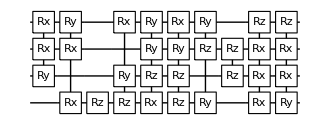

```mathematica
GetKnownCircuit["TrotterAnsatz", GetRandomPauliString[4,10], 1, 1, x] // DrawCircuit
```

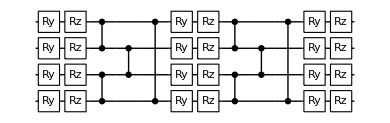

```mathematica
GetKnownCircuit["HardwareEfficientAnsatz", 2, x, 4] // DrawCircuit
```

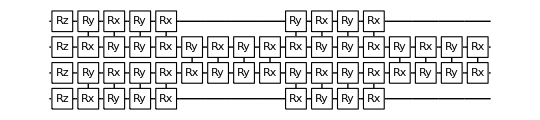

```mathematica
GetKnownCircuit["LowDepthAnsatz", 2, x, 4] // DrawCircuit
```

### ApplyCircuitDerivs

ApplyCircuitDerivs (replacing the previously named CalcQuregDerivs) can now accept any continuously parametrized circuit or channel!

```mathematica
?ApplyCircuitDerivs
```

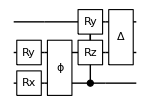

```mathematica
inρ = CreateDensityQureg[3] // InitPlusState;
dρ = CreateDensityQuregs[3,3];
u = Circuit[ Subscript[Rx, 0][a] Subscript[Ry, 1][b^2-a]Subscript[Deph, 0,1][c a] Subscript[C, 0][R[c/a, Subscript[Z, 1] Subscript[Y, 2]]] Subscript[Depol, 1,2][a-b+c]];

DrawCircuit[u]
```

```mathematica
ApplyCircuitDerivs[inρ, u, {a->.3, b->.4, c->.5}, dρ];
GetQuregMatrix @ dρ[[1]] //Chop // MatrixForm
```

(0.0523597 | 0.39998 | -0.160934 | -0.216647 | -0.0809736 | -0.156116 | -0.160934 | 0.233672
0.39998 | 0.0895311 | 0.233672 | 0.329359 | 0.26444 | 0.459375 | 0.233672 | -0.0309304
-0.160934 | 0.233672 | -0.0523597 | -0.123092 | -0.160934 | -0.216647 | -0.185693 | 0.206428
-0.216647 | 0.329359 | -0.123092 | -0.204406 | -0.216647 | -0.290937 | -0.258633 | 0.358791
-0.0809736 | 0.26444 | -0.160934 | -0.216647 | 0.0523597 | -0.0205754 | -0.160934 | 0.233672
-0.156116 | 0.459375 | -0.216647 | -0.290937 | -0.0205754 | 0.0151884 | -0.216647 | 0.329359
-0.160934 | 0.233672 | -0.185693 | -0.258633 | -0.160934 | -0.216647 | -0.0523597 | 0.341968
0.233672 | -0.0309304 | 0.206428 | 0.358791 | 0.233672 | 0.329359 | 0.341968 | 0.0996868)

### CalcExpecPauliStringDerivs

CalcExpecPauliStringDerivs rapidly computes the gradient of a variational observable without having to create dedicated statevectors like above, using a novel algorithm (https://arxiv.org/abs/2009.02823). This returns the quantity:

	∇_θ_i inψ(û[θ⃗])^†  ĥ  û[θ⃗] inψ

It can furthermore compute the gradient of noisy channels upon density matrices (using another novel algorithm, see Ch5.7 of https://pdfhost.io/v/khdW2GJgP_Thesis_Tyson_Jones). In this instance, it returns:

	∇_θ_i Trace[ĥ   channel_(θ⃗){inρ}]

These quantities appear in many quantum variational algorithms like quantum gradient descent, quantum natural gradient and variational imaginary time evolution. Parameters can be repeated between gates, gates can be multi-parameterised, and feature arbitrary (albeit continuous) functions of the variational parameters.

```mathematica
?CalcExpecPauliStringDerivs
```

```mathematica
DrawCircuit[u]
```

-Graphics-

```mathematica
h = .5 Subscript[X, 0] Subscript[Y, 1] +Subscript[Z, 0] Subscript[Z, 1]+ Subscript[Z, 0]+2 Subscript[Z, 2]-4 Subscript[Z, 1]-.3 Subscript[X, 1] Subscript[Z, 2] + Subscript[Y, 0] Subscript[Y, 1] Subscript[Y, 2] + .2 Subscript[X, 0] Subscript[X, 2] Subscript[X, 1];

CalcExpecPauliStringDerivs[inρ, u, {a->.4, b->.2, c->.5}, h]
```

{0.650992,-1.26729,1.6246}

Let’s compare the first element to its analytic form:

```mathematica
D[Tr[CalcPauliExpressionMatrix[h] . Transpose @ ArrayReshape[CalcCircuitMatrix[u] .  Flatten @ Transpose @ GetQuregMatrix[inρ], {2^3,2^3}]], a] /.  {a->.4, b->.2, c->.5}
```

0.650992+0. ⅈ

### CalcMetricTensor

CalcMetricTensor rapidly computes the metric tensor of the given parameterised circuit or channel. If a pure circuit is given, this function returns the quantum geometric tensor like that appearing in quantum natural gradient and variational imaginary time evolution:

	G_ij =(∂ψ[θ⃗])/(∂θ_i)(∂ψ[θ⃗])/(∂θ_j) - (∂ψ[θ⃗])/(∂θ_i)ψ[θ⃗]ψ[θ⃗](∂ψ[θ⃗])/(∂θ_j)          where	 ψ[θ⃗]=û[θ⃗] inψ .

When a noisy channel is given, this function returns the Hilbert-Schmidt derivative metric

	M_ij = 1/2 Tr[  (∂ ρ[θ⃗])/(∂θ_i)  (∂ ρ[θ⃗])/(∂θ_j)  ]         where	 ρ[θ⃗] =channel_(θ⃗){ inρ }  ,

which in many settings well approximates the quantum Fisher information matrix and can replace it in quantum natural gradient for a superior noise-aware minimisation.

```mathematica
?CalcMetricTensor
```

```mathematica
u
DrawCircuit[u]
```

{Rx_0[a],Ry_1[-a+b^2],Deph_(0,1)[a c],C_0[R[c/a,Y_2 Z_1]],Depol_(1,2)[a-b+c]}

-Graphics-

```mathematica
CalcMetricTensor[inρ, u, {a->.1,b->.2,c->.3}] // Chop // MatrixForm
```

(142.846 | -1.39051 | -45.6214
-1.39051 | 0.974851 | -0.974446
-45.6214 | -0.974446 | 16.6879)

These functions make variational simulation trivial. We here demonstrate noise-aware quantum natural gradient, whereby dephasing noise strength is correlated with the prior gate parameter.

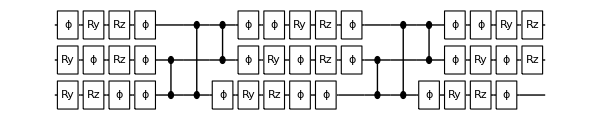

```mathematica
u = GetKnownCircuit["HardwareEfficientAnsatz", 2, θ, 3];
i = 1;
u = Riffle[Partition[u,3], ConstantArray[Table[Subscript[Deph, q][.2 + 10^-4 θ[i++]],{q,0,2}], Length[u]]] // Flatten;
DrawCircuit[u]
```

```mathematica
{ρ, inρ, wρ} = CreateDensityQuregs[3, 3];
InitPlusState[inρ];
```

If one foregoes measuring the energy, then each iteration of minimisation requires only three function calls!

```mathematica
Δt = .01;
nt = 50;
θVals = Table[θ[i]->RandomReal[],{i,u[[-1,1,1]]}];

eVals = Table[
	v = CalcExpecPauliStringDerivs[inρ, u, θVals, h];
	m = CalcMetricTensor[inρ, u, θVals] // Chop;

	Δθ = Fit[{m,v}, FitRegularization->{"Tikhonov",10^-4}];
	θVals[[All,2]] += - Δθ Δt ;

	ApplyCircuit[CloneQureg[ρ,inρ], u /. θVals];
	CalcExpecPauliString[ρ,h, wρ],

	nt
];
```

Here is how the energy evolved

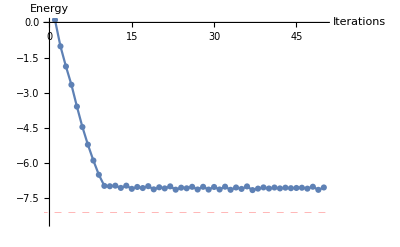

```mathematica
eMin = CalcPauliStringMinEigVal[h];

ListLinePlot[eVals, 
	AxesLabel-> {"Iterations", "Energy"},
	PlotRange->{0,1.05 eMin}, 
	PlotMarkers->Automatic, 
	GridLines->{{},{{eMin,Directive[Red,Dashed]}}}
]
```

### Error reporting

Functions which process circuits can now precisely report the erroneous operator.

```mathematica
CalcCircuitMatrix[Subscript[J, 0]]
```

CalcCircuitMatrix::error: Circuit contained an unrecognised or unsupported gate: J_0

$Failed

```mathematica
ApplyCircuit[CreateQureg[2], Circuit[Subscript[X, 3]]]
```

ApplyCircuit::error: Cannot simulate X_3. Invalid target qubit. Must be >=0 and <numQubits. The qureg (id 7) has been restored to its prior state.

$Failed

```mathematica
ApplyCircuit[CreateQureg[2], Subscript[U, 0][({{0, 1}, {2, 3}})]]
```

ApplyCircuit::error: Cannot simulate U_0[(0 | 1
2 | 3)]. Matrix is not unitary. The qureg (id 8) has been restored to its prior state.

$Failed

### GetRandomPauliString

```mathematica
?GetRandomPauliString
```

```mathematica
GetRandomPauliString[3, 10]
```

0.940567 Y_0+0.0133663 X_0 Y_2+0.407032 X_1 Y_2-0.240966 X_1 Y_0 Y_2-0.458556 X_0 Y_2 Z_1+0.600443 Z_0 Z_1+0.502558 Z_2-0.756216 X_0 Z_2-0.077569 X_1 Y_0 Z_2-0.341494 Z_0 Z_1 Z_2

```mathematica
GetRandomPauliString[2, 10^5, {0,1}]
```

GetRandomPauliString::error: More terms were requested than there are unique Pauli tensors. Hide this warning with Quiet[].

0.508625 Id_0 Id_1+0.33438 X_0+0.488285 X_1+0.554076 X_0 X_1+0.663799 Y_0+0.846016 X_1 Y_0+0.669192 Y_1+0.868138 X_0 Y_1+0.0866329 Y_0 Y_1+0.731169 Z_0+0.199964 X_1 Z_0+0.0695654 Y_1 Z_0+0.365943 Z_1+0.762892 X_0 Z_1+0.686691 Y_0 Z_1+0.145336 Z_0 Z_1

### CalcPauliStringMinEigVal

```mathematica
?CalcPauliStringMinEigVal
```

```mathematica
CalcPauliStringMinEigVal @ GetRandomPauliString[15, 10]
```

-2.9193

By using sparse matrices, this function will require exponentially less memory and be be significantly faster than alternative methods (like Min @ Eigenvalues @ CalcPauliStringMatrix[h]) when run on large systems (e.g. 15 qubits) with few terms.

### SetQuregToPauliString

```mathematica
?SetQuregToPauliString
```

```mathematica
h = GetRandomPauliString[3, 3]
CalcPauliExpressionMatrix[h] //Chop// MatrixForm
```

-0.332144 X_1 X_2+0.732511 X_0 Y_1 Z_2+0.136264 X_1 Z_0 Z_2

(0 | 0 | 0.136264 | 0.-0.732511 ⅈ | 0 | 0 | -0.332144 | 0
0 | 0 | 0.-0.732511 ⅈ | -0.136264 | 0 | 0 | 0 | -0.332144
0.136264 | 0.+0.732511 ⅈ | 0 | 0 | -0.332144 | 0 | 0 | 0
0.+0.732511 ⅈ | -0.136264 | 0 | 0 | 0 | -0.332144 | 0 | 0
0 | 0 | -0.332144 | 0 | 0 | 0 | -0.136264 | 0.+0.732511 ⅈ
0 | 0 | 0 | -0.332144 | 0 | 0 | 0.+0.732511 ⅈ | 0.136264
-0.332144 | 0 | 0 | 0 | -0.136264 | 0.-0.732511 ⅈ | 0 | 0
0 | -0.332144 | 0 | 0 | 0.-0.732511 ⅈ | 0.136264 | 0 | 0)

```mathematica
ρ = CreateDensityQureg[3];
SetQuregToPauliString[ρ, h];
GetQuregMatrix[ρ] // Chop // MatrixForm
```

(0 | 0 | 0.136264 | 0.-0.732511 ⅈ | 0 | 0 | -0.332144 | 0
0 | 0 | 0.-0.732511 ⅈ | -0.136264 | 0 | 0 | 0 | -0.332144
0.136264 | 0.+0.732511 ⅈ | 0 | 0 | -0.332144 | 0 | 0 | 0
0.+0.732511 ⅈ | -0.136264 | 0 | 0 | 0 | -0.332144 | 0 | 0
0 | 0 | -0.332144 | 0 | 0 | 0 | -0.136264 | 0.+0.732511 ⅈ
0 | 0 | 0 | -0.332144 | 0 | 0 | 0.+0.732511 ⅈ | 0.136264
-0.332144 | 0 | 0 | 0 | -0.136264 | 0.-0.732511 ⅈ | 0 | 0
0 | -0.332144 | 0 | 0 | 0.-0.732511 ⅈ | 0.136264 | 0 | 0)

### SampleClassicalShadow

SampleClassicalShadow encodes a density matrix into a number of sampled Pauli product outcomes, as per this paper.

```mathematica
?SampleClassicalShadow
```

```mathematica
ρ = InitPlusState @ CreateDensityQureg[3];
ApplyCircuit[ρ, u /. {a->.4, b->.2, c->.5}];

SampleClassicalShadow[ρ, 5] // Column
```

ApplyCircuit::error: Circuit contains non-numerical or non-real parameters!

{{2,1,2},{0,0,1}}
{{2,1,2},{1,0,0}}
{{2,1,1},{1,0,0}}
{{3,2,2},{1,0,0}}
{{3,3,2},{1,0,0}}

### New gates

```mathematica
?Fac
```

```mathematica
?UNonNorm
```

```mathematica
?Matr
```

## Changes

### CalcDensityInnerProduct(s)

CalcDensityInnerProduct(s) now return complex scalars, capturing the full Hilbert-Schmidt scalar product when the input density matrices are not normalised.

```mathematica
?CalcDensityInnerProduct
```

```mathematica
{a,b} = CreateDensityQuregs[3,2];
SetQuregMatrix[a, RandomVariate @ CircularSymplecticMatrixDistribution @ 4];

CalcDensityInnerProduct[a,b]
```

-0.190231+0.393956 ⅈ

### Mix* deprecated

All explicit mixing functions like MixDamping have been deprecated, since they are more concisely invoked with ApplyCircuit.

```mathematica
?MixTwoQubitDephasing
```

These deprecated functions are still callable for backwards compatibility

```mathematica
MixTwoQubitDepolarising[b, 0,1,.5];
CalcPurity[b]
```

ApplyCircuit::error: The function MixTwoQubitDepolarising[] is deprecated, though has still been performed. In future, please use ApplyCircuit[] with the Depol[] gate instead, or temporarily hide this message using Quiet[].

0.413333

### PauliSum -> PauliString

Any reference to PauliSum in the QuESTlink API has been renamed to PauliString.

```mathematica
?CalcExpecPauliSum
```

These deprecated functions are still callable for backwards compatibility

```mathematica
CalcExpecPauliSum[a,GetRandomPauliString[3],b]
```

CalcExpecPauliString::error: The function CalcExpecPauliSum[] is deprecated. Use CalcExpecPauliString[] or temporarily hide this message using Quiet[].

-2.61389

### CalcPauliExpressionMatrix

CalcPauliExpressionMatrix now returns a sparse matrix for more efficient handling of large operators, especially symbolic ones with few terms.

```mathematica
CalcPauliExpressionMatrix @ GetRandomPauliString[10,10]
```

SparseArray[…]

CalcPauliStringMatrix remains useful for (significantly) faster parallel handling of numerical real-coefficient operators.

### AssertValidChannels

By default, functions like CalcCircuitMatrix will now assert that the given decoherence channels are completely-positive and trace-preserving, and infer assumptions about their parameters which are then used to simplify subsequent expressions. This behaviour can be disabled with AssertValidChannels -> False.

```mathematica
?AssertValidChannels
```

```mathematica
CalcCircuitMatrix[Subscript[Depol, 0][x]] // MatrixForm
```

(1-(2 x)/3 | 0 | 0 | (2 x)/3
0 | 1-(4 x)/3 | 0 | 0
0 | 0 | 1-(4 x)/3 | 0
(2 x)/3 | 0 | 0 | 1-(2 x)/3)

```mathematica
CalcCircuitMatrix[Subscript[Depol, 0][x], AssertValidChannels->False] // MatrixForm
```

(√(1-x) Conjugate[√(1-x)]+1/3 √x Conjugate[√x] | 0 | 0 | 2/3 √x Conjugate[√x]
0 | √(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x] | 0 | 0
0 | 0 | √(1-x) Conjugate[√(1-x)]-1/3 √x Conjugate[√x] | 0
2/3 √x Conjugate[√x] | 0 | 0 | √(1-x) Conjugate[√(1-x)]+1/3 √x Conjugate[√x])

### DrawCircuit

DrawCircuit will now render global phase gates (G) and the identity suboperators of Pauli gadgets R

```mathematica
DrawCircuit @ Circuit[G[θ] R[π, Subscript[X, 0] Subscript[Id, 1] Subscript[Z, 2]]  ]
```

-Graphics-

### UNonNorm and Matr

Previously, Matr was a normalisation-relaxed form of the restrictedly-unitary operator U. Now, UNonNorm fills that role while Matr is never assumed nor treated as a unitary. This means that when applied to density-matrices, Matr will only ever left-multiply (never being conjugated and right-multiplied like UNonNorm).

```mathematica
?Matr
?UNonNorm
```

### CalcQuregDerivs -> ApplyCircuitDerivs

CalcQuregDerivs has been renamed to ApplyCircuitDerivs, along with its significant extensions as per above. Note too that the order of the arguments changed.

```mathematica
?CalcQuregDerivs
```